# Lista 1 - Introdução à Física Computacional I

## Marcos Vinícius Rodrigues Ribeiro

## Problema 1.1

A posição inicial é dada no enunciado como “a”, do qual é um raio de órbita inicial. No contexto de uma partícula em um potencial central, para existir um movimento circular a força que age neste sistema tem de ser igual a força centrípeta, o que leva a seguinte igualdade:

                                                                                                               mv_0^2/a=k/a^β⇒v_0=√(k/ma^(β-1))

## Problema 1.2

Expressando as equações diferenciais e antes disso aplicar a igualdade do enuncidado onde: m = k = a =  1. Para resolver essas EDO’s de numericamente é utilizado a função NDSolve, onde os argumentos incluem a equação que será resolvida e as condições iniciais do sistema. Também é necessário um intervalo onde será aplicado a aproximação. O período nada mais é que é a razão entre o tamanho da órbita e v_0.

```mathematica
eq1 = m*x''[t]==-(k*x[t])/((√(x[t]^2+y[t]^2))^(1+β))/.{m->1,k->1,a->1};
```

```mathematica
eq2 = m*y''[t]==-(k*y[t])/((√(x[t]^2+y[t]^2))^(1+β))/.{m->1,k->1,a->1};

v0 = (k/(m*a^(β-1)))^(1/2)/.{m->1,k->1,a->1};
tempoPeriodo=(2π*a)/v0/.{m->1,k->1,a->1};
solProblema1=NDSolve[{eq1 /.β->2,eq2 /.β->2,x'[0]==0,y'[0]==v0,x[0]==1,y[0]==0},{x,y},{t,0,4*tempoPeriodo}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

Utilizando a ParametricPlot para gerar o gráfico de x(t) e y(t) através da aproximação numérica e incluindo a função Evaluate, este procedimento inicialmente adquire as soluções provenientes da variável “solProblema1” e, em seguida, computa as funções numéricas decorrentes dessas soluções, permitindo sua aplicação subsequente no ParametricPlot. Também foi incluída uma série de configurações de visual na variável “design”.

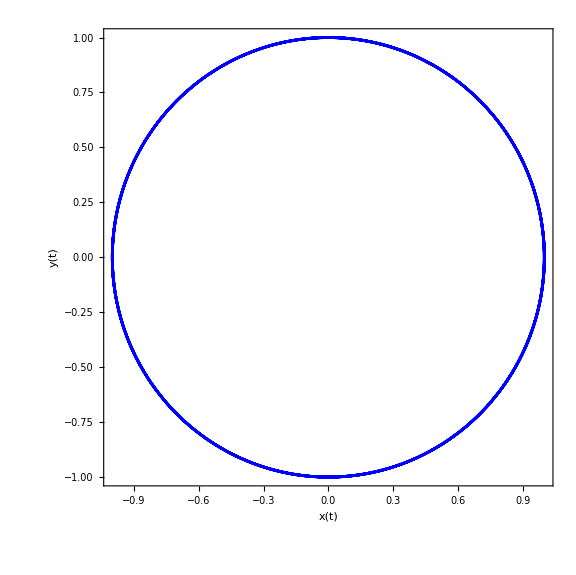

```mathematica
design={ImageSize->Large,LabelStyle->Medium,Frame->True,PlotStyle->Blue,FrameStyle->Black};
ParametricPlot[{Evaluate[{x[t],y[t]}/.solProblema1]},{t,0,4*tempoPeriodo},Evaluate[design],FrameLabel->{{"y(t)","y(t)"},{"x(t)","Gráfico da órbita circular(β = 2)"}}]
```

Fazendo gráfico com a diminuição ou aumento da velocidade. Primeiro com um aumento de 0.5 e em seguida com a redução de mesma quantidade.

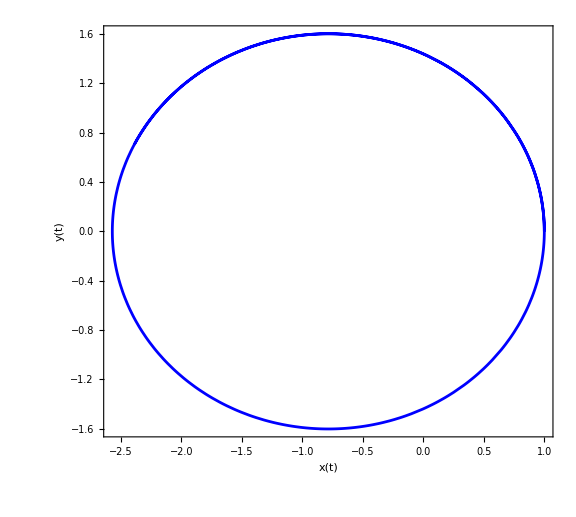

```mathematica
tempoPeriodo2=(2π*a)/(v0+0.2)/.{m->1,k->1,a->1};
solPr1V0Maior=NDSolve[{eq1 /.β->2,eq2 /.β->2,x'[0]==0,y'[0]==v0+0.2,x[0]==1,y[0]==0},{x,y},{t,0,4*tempoPeriodo2}];

design={ImageSize->Large,LabelStyle->Medium,Frame->True,PlotStyle->Blue,FrameStyle->Black};
ParametricPlot[{Evaluate[{x[t],y[t]}/.solPr1V0Maior]},{t,0,4*tempoPeriodo2},Evaluate[design],FrameLabel->{{"y(t)","y(t)"},{"x(t)","Gráfico da órbita circular(β = 2 e v_0+0.2)"}}]
```

Agora com a redução:

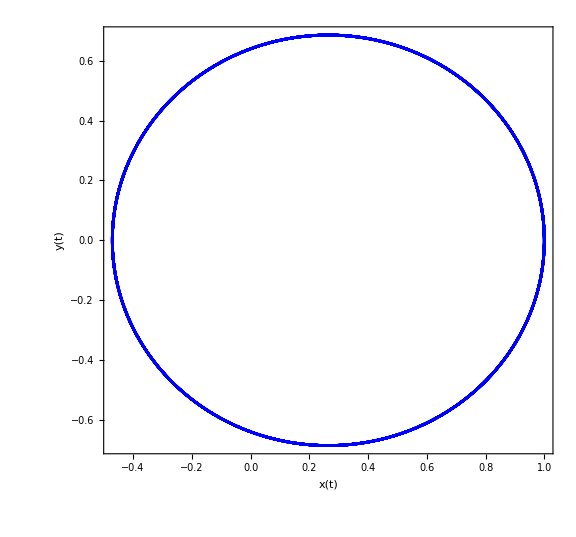

```mathematica
tempoPeriodo3=(2π*a)/(v0-0.2)/.{m->1,k->1,a->1};
solPr1V0Menor=NDSolve[{eq1 /.β->2,eq2 /.β->2,x'[0]==0,y'[0]==v0-0.2,x[0]==1,y[0]==0},{x,y},{t,0,4*tempoPeriodo3}];

design={ImageSize->Large,LabelStyle->Medium,Frame->True,PlotStyle->Blue,FrameStyle->Black};
ParametricPlot[{Evaluate[{x[t],y[t]}/.solPr1V0Menor]},{t,0,4*tempoPeriodo3},Evaluate[design],FrameLabel->{{"y(t)","y(t)"},{"x(t)","Gráfico da órbita circular(β = 2 e v_0+0.2)"}}]
```

## Problema 1.3

Agora tomando β = 3 e efetuando os mesmos cálculos do item anterior, utilizando NDSolve para resolver de forma numérica e utilizando a ParametricPlot para gerar os gráficos das órbitas, chamei as soluções desse item de “solPr1i3”, e nas outras variáveis adicionei “i3” para indicar o item:

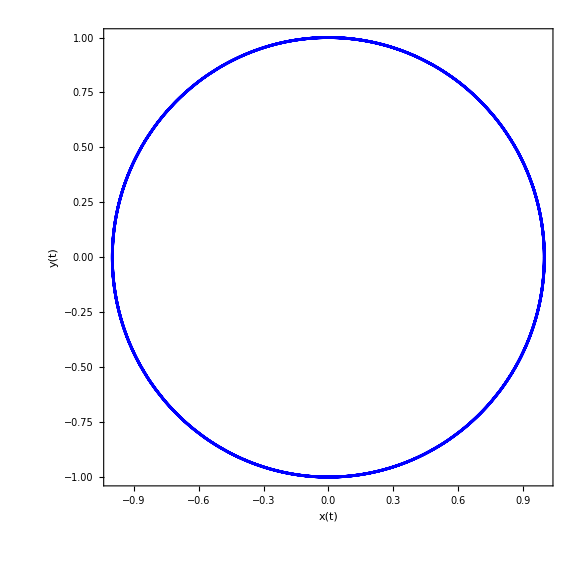

```mathematica
v0i3 = (k/(m*a^(β-1)))^(1/2)/.{m->1,k->1,a->1,β->3};
tempoPeriodoP1i3=(2π*a)/v0i3/.{m->1,k->1,a->1};
solPr1i3=NDSolve[{eq1 /.β->3,eq2 /.β->3,x'[0]==0,y'[0]==v0i3,x[0]==1,y[0]==0},{x,y},{t,0,4*tempoPeriodoP1i3}];

design={ImageSize->Large,LabelStyle->Medium,Frame->True,PlotStyle->Blue,FrameStyle->Black};
ParametricPlot[{Evaluate[{x[t],y[t]}/.solPr1i3]},{t,0,4*tempoPeriodoP1i3},Evaluate[design],FrameLabel->{{"y(t)","y(t)"},{"x(t)","Gráfico da órbita circular(β = 3)"}}]
```

Verificado que o novo valor de v_0 gera uma órbita circular, a análise para valores maiores ou menores de v_0 é feita utilizando a NDSolve novamente e a ParametricPlot. Primeiro para uma velocidade inicial menor e em seguida uma velocidade maior.

## Problema 1.4

De forma análoga aos itens anteriores, com alteração apenas dos parâmetro v0 e β.

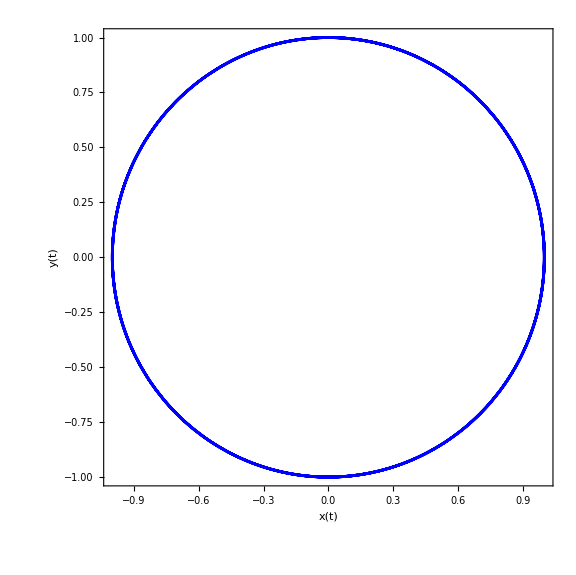

```mathematica
PeriodoP1i4=(2π*a)/v0/.{m->1,k->1,a->1};
soli4=NDSolve[{eq1 /.β->-2,eq2 /.β->-2,x'[0]==0,y'[0]==v0,x[0]==1,y[0]==0},{x,y},{t,0,4*PeriodoP1i4}];
ParametricPlot[{Evaluate[{x[t],y[t]}/.soli4]},{t,0,4*PeriodoP1i4},Evaluate[design],FrameLabel->{{"y(t)","y(t)"},{"x(t)","Gráfico da de órbita circular com β = -2"}}]
```

## Problema 2.1

Colocando as condições do enunciado ( z=0, ou seja, θ=π/2), o seno se torna 1 e tomando A = c = ω/2π = 1, o módulo do campo elétrico se torna:

```mathematica
e[t_,x_,y_]:= √((1/(√(x^2+y^2))Cos[2π(t-√(x^2+y^2))])^2);
```

Para criar a animação é necessário gráficos de densidade do campo, que .08são obtidos pela função DensityPlot, impondo os intervalos de x e y (colocando de -1 a 1) e utilizando 100 pontos para obter uma boa resolução.

```mathematica
DensityPlot[e[0,x,y],{x,-1,1},{y,-1,1},PlotLegends->Automatic,PlotPoints->100]
```

-Graphics-

## Problema 2.2

Para encontrar o intervalo dos quadros é necessário dividir o período do movimento, que é 1 segundo, por 24.  A função Table produz uma lista de imagens ao longo do intervalo de tempo ‘t’ especificado na chamada da função. Os mesmos intervalos de ‘x’ e ‘y’ foram mantidos para todas as imagens, assim como o número constante de pontos por quadro. As imagens foram geradas ao longo de um intervalo durante o movimento.

Por fim, a função ListAnimate anima a sequência de imagens armazenadas na tabela.

```mathematica
tquadro=1/24;
quadros = Table[DensityPlot[e[t,x,y],{x,-1,1},{y,-1,1},PlotLegends->Automatic,PlotPoints->100],{t,0,24*tquadro,tquadro}];
ListAnimate[imagens]
```

ListAnimate[imagens]

Foi utilizado o comando para criar o gif e depois foi exportado.

## Problema 3.1

Para gerar os  n = 2^10  valores pseudoaleatórios no intervalo de 0 a 2 foi utilizado a função RandomReal. Para obter a média do polinômio no intervalo foi utilizado a função Mean e foi calculada o valor aproximado da integral:

```mathematica
a = 0;
b=2; 
n = 2^10; 
xvalores = RandomReal[{a,b},n];
fvalores = 6*xvalores-3*xvalores^2;
mediaf = Mean[fvalores];
aproximInt = (b-a)*mediaf (*Integral aproximada*)
```

4.08169

O valor exato da integral é obtido trivialmente (integração de polinômio), e é exatamente 4. Calculando o módulo da diferença com a função Abs:

```mathematica
vexato=4;
diff= Abs[aproximInt-vexato]
```

0.0816905

## Problema 3.2

De forma totalmente análoga ao item anterior:

```mathematica
n2=2^20; 
xvalores2 = RandomReal[{a,b},n2];
fvalores2 = 6*xvalores2-3*xvalores2^2;
mediaf2 = Mean[fvalores2];
aproximInt2 = (b-a)*mediaf2 (*Integral aproximada*)
```

3.99946

```mathematica
diff= Abs[aproximInt2-vexato]
```

0.000544564

A precisão aumentou muito, um erro da ordem da quarta casa decimal em comparação com um erro anterior na segunda casa decimal. Importante destacar o aumento considerável de números sorteados, sendo a nova quantidade 10 ordens de grandeza maior, aumentando o custo de processamento.

## Problema 3.3

Para repetir 100 vezes o cálculo análogo ao dois itens anteriores é feito um laço com a função Do, onde o valor de m = 100 define quantas vezes o .08laço será repetido. A função AppendTo é utilizada com o intuito de adicionar cada valor aproximado de integral à lista aproxisInts.
A média é calculada com a função Mean, aplicada aos valores de aproxisInts. O desvio-padrão é obtido com a função StandardDeviation, que só necessita da lista como argumento.

```mathematica
m=100;
n3=2^10;
aproxisInts = {};
Do[xvalores3 = RandomReal[{a,b},n];
fvalores3 = 6*xvalores3-3*xvalores3^2;
mediaf3 = Mean[fvalores3];
AppendTo[aproxisInts,(b-a)*mediaf3 ] ,m]
mediaM3= Mean[aproxisInts]
desvpadM = StandardDeviation[aproxisInts]
```

4.00007

0.0545795

## Problema 3.4

Este item é feito com o cálculo análogo do item anterior com exceção de que n = 2^20.

```mathematica
n4=2^20;
aproxisInts2 = {};
Do[xvalores4 = RandomReal[{a,b},n4];
fvalores4 = 6*xvalores4-3*xvalores4^2;
mediaf4 = Mean[fvalores4];
AppendTo[aproxisInts2,(b-a)*mediaf4 ] ,m]
mediaM2 = Mean[aproxisInts2]
desvpadM2 = StandardDeviation[aproxisInts2]
```

4.00018

0.00157954

Neste caso houve uma redução significativa no valor do desvio padrão, mas a um alto custo de processamento.

## Problema 3.5

Para produzir a automação enunciada, um laço adicional da função Do é necessário, onde o valor de operações será um n = 2^i, com o i sendo acrescido em um a cada vez que o laço é percorrido. E os valores de média e desvio-padrão foram armazenados nas listas indicadas no enunciado.

```mathematica
aproxVMedios = {}; 
desvPads= {};
Do[n5=2^i;
aproxisInts5 = {};
Do[xvalores5 = RandomReal[{a,b},n5];
fvalores5 = 6*xvalores5-3*xvalores5^2;
mediaf5 = Mean[fvalores5];
AppendTo[aproxisInts5,(b-a)*mediaf5 ] ,m];
AppendTo[aproxVMedios,{n5,Mean[aproxisInts5]}];
AppendTo[desvPads,{n5,StandardDeviation[aproxisInts5]}],{i,10,20}]
```

Como cada valor de média e desvio-padrão possui um valor de n correspondente, os valores podem ser colocados em um gráfico, com os valores médios de cada integral em função da potência ao qual o dois foi elevado. Para gerar um gráfico com os valores das listas, foi utilizada a ListLogLogPlot, que gera o gráfico em escala logarítmica.

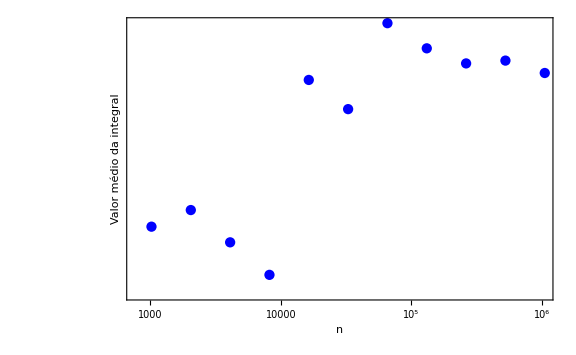

```mathematica
graficoMedias = ListLogLogPlot[aproxVMedios,PlotStyle->Blue,Evaluate[{ImageSize->Large,LabelStyle->Medium,Axes->True,Frame->True}],FrameLabel->{"n","Valor médio da integral"},FrameStyle->Black]
```

Gerando o gráfico dos desvios-padrão.

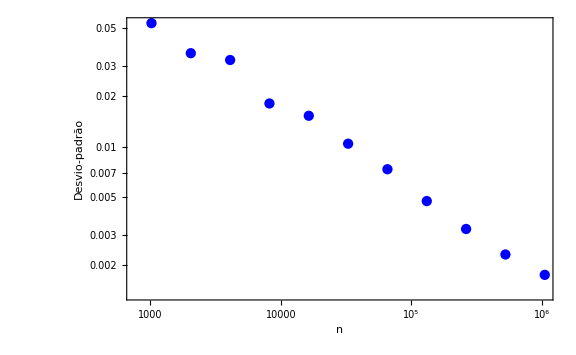

```mathematica
graficoDesvPads = ListLogLogPlot[desvPads,PlotStyle->Blue,Evaluate[{ImageSize->Large,LabelStyle->Medium,Axes->True,Frame->True}],FrameLabel->{"n","Desvio-padrão"},FrameStyle->Black]
```

## Problema 3.6

Gerando o gráfico com o ListPlot para não utilizar os eixos logarítmicos. Essa função pode utilizar uma lista de pares ordenados para gerar pontos em um gráficos, neste caso o n será plotado no eixo x e os valores de desvio-padrão no eixo y.

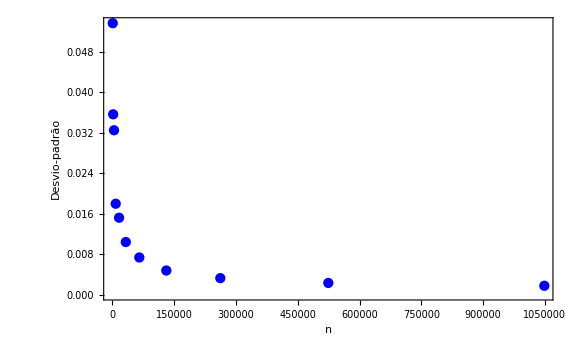

```mathematica
graficoDesvPads = ListPlot[desvPads,PlotStyle->Blue,Evaluate[{ImageSize->Large,LabelStyle->Medium,Axes->True,Frame->True}],FrameLabel->{"n","Desvio-padrão"},FrameStyle->Black]
```

O ajuste indicado pelo enunciado é da forma a/n^b, para tratar deste ajuste não linear será utilizada a função FindFit, que possui como argumentos o conjunto de dados, em seguida a forma do ajuste.